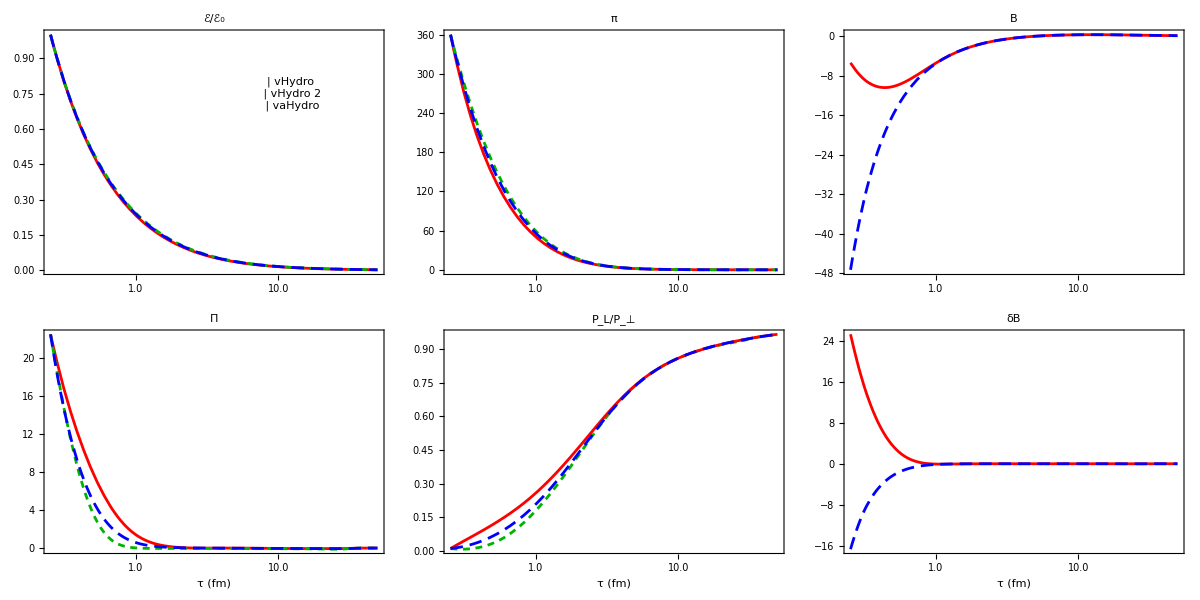

0.01

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

stylesVH={Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]};

stylesVH2={Directive[RGBColor[0,0.7,0],AbsoluteThickness[2],AbsoluteDashing[{5,4}]]};

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};


(*//////////////////////////////////////////////////////////////*)

EnergyDensityDataRawVH=Import[wd<>"/eplot_vh.dat"];
piDataRawVH=Import[wd<>"/piplot_vh.dat"];
PiDataRawVH=Import[wd<>"/bulkplot_vh.dat"];
plptDataRawVH=Import[wd<>"/plptplot_vh.dat"];


EnergyDensityDataVH= Take[EnergyDensityDataRawVH,{2,Length[EnergyDensityDataRawVH]}];
piDataVH= Take[piDataRawVH,{2,Length[piDataRawVH]}];
PiDataVH= Take[PiDataRawVH,{2,Length[PiDataRawVH]}];
plptDataVH= Take[plptDataRawVH,{2,Length[plptDataRawVH]}];

energydensityVH = Interpolation[EnergyDensityDataVH[[All,{1,2}]]];
piVH = Interpolation[piDataVH[[All,{1,2}]]];
bulkVH = Interpolation[PiDataVH[[All,{1,2}]]];
plptVH = Interpolation[plptDataVH[[All,{1,2}]]];



(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVH2=Import[wd<>"/eplot_vh_limit.dat"];
piDataRawVH2=Import[wd<>"/piplot_vh_limit.dat"];
PiDataRawVH2=Import[wd<>"/bulkplot_vh_limit.dat"];
plptDataRawVH2=Import[wd<>"/plptplot_vh_limit.dat"];


EnergyDensityDataVH2= Take[EnergyDensityDataRawVH2,{2,Length[EnergyDensityDataRawVH2]}];
piDataVH2= Take[piDataRawVH2,{2,Length[piDataRawVH2]}];
PiDataVH2= Take[PiDataRawVH2,{2,Length[PiDataRawVH2]}];
plptDataVH2= Take[plptDataRawVH2,{2,Length[plptDataRawVH2]}];

energydensityVH2 = Interpolation[EnergyDensityDataVH2[[All,{1,2}]]];
piVH2 = Interpolation[piDataVH2[[All,{1,2}]]];
bulkVH2 = Interpolation[PiDataVH2[[All,{1,2}]]];
plptVH2 = Interpolation[plptDataVH2[[All,{1,2}]]];


(*//////////////////////////////////////////////////////////////*)
(*NAVIER STOKES*)

PiNSDataRawVH=Import[wd<>"/bulkNSplot.dat"];
PiNSDataVH= Take[PiNSDataRawVH,{2,Length[PiNSDataRawVH]}];
bulkNSVH = Interpolation[PiNSDataVH[[All,{1,2}]]];

piNSDataRawVH=Import[wd<>"/piNSplot.dat"];
piNSDataVH= Take[piNSDataRawVH,{2,Length[piNSDataRawVH]}];
piNSVH = Interpolation[piNSDataVH[[All,{1,2}]]];

piNSDataRawVAH=Import[wd<>"/piNSplot_vah.dat"];
piNSDataVAH= Take[piNSDataRawVAH,{2,Length[piNSDataRawVAH]}];
piNSVAH = Interpolation[piNSDataVAH[[All,{1,2}]]];
(*//////////////////////////////////////////////////////////////*)


EnergyDensityDataRawVAH=Import[wd<>"/eplot_vah.dat"];
piDataRawVAH=Import[wd<>"/piplot_vah.dat"];
PiDataRawVAH=Import[wd<>"/bulkplot_vah.dat"];
plptDataRawVAH=Import[wd<>"/plptplot_vah.dat"];
BDataRawVAH=Import[wd<>"/Bplot_vah.dat"];
BeqDataRawVAH=Import[wd<>"/Beqplot_vah.dat"];
dB2ndDataRawVAH=Import[wd<>"/dB2ndplot_vah.dat"];

EnergyDensityDataVAH= Take[EnergyDensityDataRawVAH,{2,Length[EnergyDensityDataRawVAH]}];
piDataVAH= Take[piDataRawVAH,{2,Length[piDataRawVAH]}];
PiDataVAH= Take[PiDataRawVAH,{2,Length[PiDataRawVAH]}];
plptDataVAH= Take[plptDataRawVAH,{2,Length[plptDataRawVAH]}];
BDataVAH= Take[BDataRawVAH,{2,Length[BDataRawVAH]}];
BeqDataVAH= Take[BeqDataRawVAH,{2,Length[BeqDataRawVAH]}];
dB2ndDataVAH= Take[dB2ndDataRawVAH,{2,Length[dB2ndDataRawVAH]}];


energydensityVAH = Interpolation[EnergyDensityDataVAH[[All,{1,2}]]];
piVAH = Interpolation[piDataVAH[[All,{1,2}]]];
bulkVAH = Interpolation[PiDataVAH[[All,{1,2}]]];
plptVAH = Interpolation[plptDataVAH[[All,{1,2}]]];
BVAH = Interpolation[BDataVAH[[All,{1,2}]]];
BeqVAH = Interpolation[BeqDataVAH[[All,{1,2}]]];
dB2ndVAH = Interpolation[dB2ndDataVAH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)


t0 = EnergyDensityDataVAH[[1,1]];
tf = EnergyDensityDataVAH[[Length[EnergyDensityDataVAH],1]];

legend1=Panel[Grid[{{Graphics[{stylesVH[[1]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVH2[[1]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["vHydro 2",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{stylesVAH[[1]],Line[{{0,0},{1,0}}]},ImageSize->26
,AspectRatio->0.2],Style["vaHydro",FontSize->14,FontFamily->"Calibri"]}}],Background->White];

legend2=Panel[Grid[{{Graphics[{stylesVH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28,AspectRatio->0.2],Style["vHydro",FontSize->16,FontFamily->"Calibri"]},
{Graphics[{stylesVAH[[1]],Line[{{0,0},{1,0}}]},ImageSize->28
,AspectRatio->0.2],Style["vaHydro",FontSize->16,FontFamily->"Calibri"]}}],Background->White];

energyplot=LogLinearPlot[{energydensityVAH[t],energydensityVH2[t],energydensityVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH2[[1]],stylesVH[[1]]},PlotLabel->Style["ℰ/ℰ_0",FontSize->16,FontFamily->"Calibri"],ImageSize->230,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->Inset[legend1,{2.5,0.75}]];
bulkplot =LogLinearPlot[{bulkVAH[t],bulkVH2[t],bulkVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH2[[1]],stylesVH[[1]]},ImageSize->230,PlotLabel->Style["Π",FontSize->16,FontFamily->"Calibri"],FrameTicks->Automatic,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75];
piplot =LogLinearPlot[{piVAH[t],piVH2[t],piVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH2[[1]],stylesVH[[1]]},ImageSize->230,PlotLabel->Style["π",FontSize->16,FontFamily->"Calibri"],Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75];
plptplot =LogLinearPlot[{plptVH2[t],plptVAH[t],plptVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVH2[[1]],stylesVAH[[1]],stylesVH[[1]]},ImageSize->230,PlotLabel->Style["P_L/P_⊥",FontSize->16,FontFamily->"Calibri"],Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75];

Bplot = LogLinearPlot[{BVAH[t],BeqVAH[t]+dB2ndVAH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},PlotLabel->Style["B",FontSize->16,FontFamily->"Calibri"](*,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"]*),ImageSize->230,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75(*,Epilog->Inset[legend2,{2.5,-20}]*)];

dBplot=LogLinearPlot[{BVAH[t]-BeqVAH[t],dB2ndVAH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVAH[[1]],stylesVH[[1]]},PlotLabel->Style["δB",FontSize->16,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],ImageSize->230,Frame->True,Axes->False,BaseStyle->{FontSize->12},AspectRatio->0.75];

a1=Grid[{{energyplot,piplot,Bplot},{bulkplot,plptplot,dBplot}}]


Export["compare_hydro_all2.pdf",a1];

(*Export["compare_B.pdf",Bplot];*)

plptVAH[t0]
BVAH[t0]-BeqVAH[t0]-dB2ndVAH[t0];
```

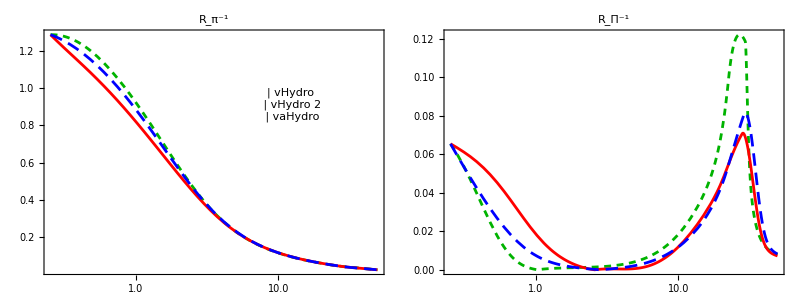

```mathematica
RpiInverseDataRawVH=Import[wd<>"/RpiInvplot_vh.dat"];
RbulkInverseDataRawVH=Import[wd<>"/RbulkInvplot_vh.dat"];

RpiInverseDataVH= Take[RpiInverseDataRawVH,{2,Length[RpiInverseDataRawVH]}];
RbulkInverseDataVH= Take[RbulkInverseDataRawVH,{2,Length[RbulkInverseDataRawVH]}];

RpiInverseVH = Interpolation[RpiInverseDataVH[[All,{1,2}]]];
RbulkInverseVH = Interpolation[RbulkInverseDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVH2=Import[wd<>"/RpiInvplot_vh_limit.dat"];
RbulkInverseDataRawVH2=Import[wd<>"/RbulkInvplot_vh_limit.dat"];

RpiInverseDataVH2= Take[RpiInverseDataRawVH2,{2,Length[RpiInverseDataRawVH2]}];
RbulkInverseDataVH2= Take[RbulkInverseDataRawVH2,{2,Length[RbulkInverseDataRawVH2]}];

RpiInverseVH2 = Interpolation[RpiInverseDataVH2[[All,{1,2}]]];
RbulkInverseVH2 = Interpolation[RbulkInverseDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

RpiInverseDataRawVAH=Import[wd<>"/RpiInvplot_vah.dat"];
RbulkInverseDataRawVAH=Import[wd<>"/RbulkInvplot_vah.dat"];

RpiInverseDataVAH= Take[RpiInverseDataRawVAH,{2,Length[RpiInverseDataRawVAH]}];
RbulkInverseDataVAH= Take[RbulkInverseDataRawVAH,{2,Length[RbulkInverseDataRawVAH]}];

RpiInverseVAH = Interpolation[RpiInverseDataVAH[[All,{1,2}]]];
RbulkInverseVAH = Interpolation[RbulkInverseDataVAH[[All,{1,2}]]];

Rpi=LogLinearPlot[{RpiInverseVH2[t],RpiInverseVAH[t],RpiInverseVH[t]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVH2[[1]],stylesVAH[[1]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->230,Frame->True,Axes->False,PlotLabel->Style["R_π^-1",FontSize->16,FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->Inset[legend1,{2.51,0.91}]];
Rbulk=LogLinearPlot[{Abs[RbulkInverseVH2[t]],Abs[RbulkInverseVAH[t]],Abs[RbulkInverseVH[t]]},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVH2[[1]],stylesVAH[[1]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,5}]]},ImageSize->230,Frame->True,Axes->False,PlotLabel->Style["R_Π^-1",FontSize->16,FontFamily->"Calibri"],(*FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],*)BaseStyle->{FontSize->12},AspectRatio->0.75];

Rplot=Grid[{{Rpi,Rbulk}}]

(*Export["compare_R.pdf",Rplot];*)
```

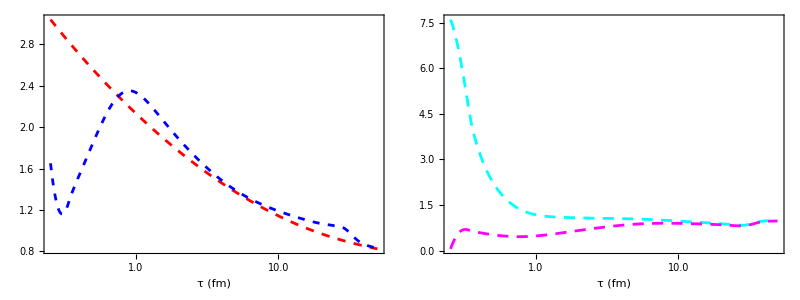

```mathematica
TDataRaw=Import[wd<>"/Tplot_vah.dat"];
lambdaDataRaw=Import[wd<>"/lambdaplot_vah.dat"];
axDataRaw=Import[wd<>"/axplot_vah.dat"];
azDataRaw=Import[wd<>"/azplot_vah.dat"];

TData= Take[TDataRaw,{2,Length[TDataRaw]}];
lambdaData= Take[lambdaDataRaw,{2,Length[lambdaDataRaw]}];
axData= Take[axDataRaw,{2,Length[axDataRaw]}];
azData= Take[azDataRaw,{2,Length[azDataRaw]}];


T = Interpolation[TData[[All,{1,2}]]];
lambda = Interpolation[lambdaData[[All,{1,2}]]];
ax = Interpolation[axData[[All,{1,2}]]];
az = Interpolation[azData[[All,{1,2}]]];

stylesVAH={Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[1,0,0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]]};

legendtemp=Panel[Grid[{{Graphics[{Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["Λ",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["T",FontSize->14,FontFamily->"Calibri"]}}],Background->White];

legendalpha=Panel[Grid[{{Graphics[{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_⊥",FontSize->14,FontFamily->"Calibri"]},
{Graphics[{Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["α_L",FontSize->14,FontFamily->"Calibri"]}}],Background->White];

temp=LogLinearPlot[{T[t],lambda[t]},{t,t0,tf},PlotRange->All,PlotStyle->{Directive[RGBColor[1,0,0],AbsoluteThickness[2],AbsoluteDashing[{6,6}]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{5,6}]]},ImageSize->235,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75(*,Epilog->Inset[legendtemp,{2.8,2.6}]*)];
alpha=LogLinearPlot[{ax[t],az[t]},{t,t0,tf},PlotRange->All,PlotStyle->{Directive[RGBColor[0,1,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[RGBColor[1,0,1],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]},ImageSize->230,Frame->True,Axes->False,FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75(*,Epilog->Inset[legendalpha,{2.8,0.67}]*)];

anisoplot=Grid[{{temp,alpha}}]

Export["aniso2.pdf",anisoplot];
```

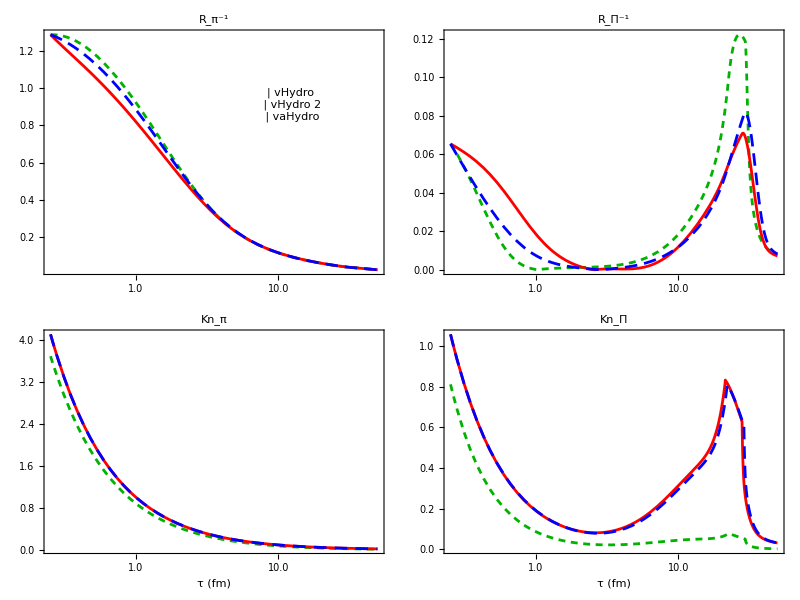

```mathematica
taupiDataRawVH=Import[wd<>"/taupiplot_vh.dat"];
taubulkDataRawVH=Import[wd<>"/taubulkplot_vh.dat"];

taupiDataVH= Take[taupiDataRawVH,{2,Length[taupiDataRawVH]}];
taubulkDataVH= Take[taubulkDataRawVH,{2,Length[taubulkDataRawVH]}];

taupiVH = Interpolation[taupiDataVH[[All,{1,2}]]];
taubulkVH = Interpolation[taubulkDataVH[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVH2=Import[wd<>"/taupiplot_vh_limit.dat"];
taubulkDataRawVH2=Import[wd<>"/taubulkplot_vh_limit.dat"];

taupiDataVH2= Take[taupiDataRawVH2,{2,Length[taupiDataRawVH2]}];
taubulkDataVH2= Take[taubulkDataRawVH2,{2,Length[taubulkDataRawVH2]}];

taupiVH2 = Interpolation[taupiDataVH2[[All,{1,2}]]];
taubulkVH2 = Interpolation[taubulkDataVH2[[All,{1,2}]]];

(*//////////////////////////////////////////////////////////////*)

taupiDataRawVAH=Import[wd<>"/taupiplot_vah.dat"];
taubulkDataRawVAH=Import[wd<>"/taubulkplot_vah.dat"];

taupiDataVAH= Take[taupiDataRawVAH,{2,Length[taupiDataRawVAH]}];
taubulkDataVAH= Take[taubulkDataRawVAH,{2,Length[taubulkDataRawVAH]}];

taupiVAH = Interpolation[taupiDataVAH[[All,{1,2}]]];
taubulkVAH = Interpolation[taubulkDataVAH[[All,{1,2}]]];

Knpi=LogLinearPlot[{Sqrt[1.5]*taupiVH2[t]/t,Sqrt[1.5]*taupiVAH[t]/t,Sqrt[1.5]*taupiVH[t]/t},{t,t0,tf},PlotRange->All,PlotStyle->{stylesVH2[[1]],stylesVAH[[1]],Directive[RGBColor[0,0,1],AbsoluteThickness[2],AbsoluteDashing[{9,6}]]},ImageSize->230,Frame->True,Axes->False,PlotLabel->Style["Kn_π",FontSize->16,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75(*,Epilog->Inset[legend1,{2.2,0.66}]*)];
Knbulk=LogLinearPlot[{taubulkVH2[t]/t,taubulkVAH[t]/t,taubulkVH[t]/t},{t,t0,tf},PlotStyle->{stylesVH2[[1]],stylesVAH[[1]],stylesVH[[1]]},ImageSize->230,Frame->True,Axes->False,PlotLabel->Style["Kn_Π",FontSize->16,FontFamily->"Calibri"],FrameLabel->Style["τ (fm)",FontFamily->"Calibri"],BaseStyle->{FontSize->12},AspectRatio->0.75];

(*Rplot=Grid[{{Knpi,Knbulk}}];

Export["compare_Kn2.pdf",Rplot];*)

a2=Grid[{{Rpi,Rbulk},{Knpi,Knbulk}}]

Export["compare_validity2.pdf",a2];
```